#### Smirnov’s theorem

```mathematica
data1=RandomVariate[NormalDistribution[2,1],400];
data2=RandomVariate[NormalDistribution[2,1],700];
```

```mathematica
empf1=EmpiricalDistribution[data1];
empf2=EmpiricalDistribution[data2];
```

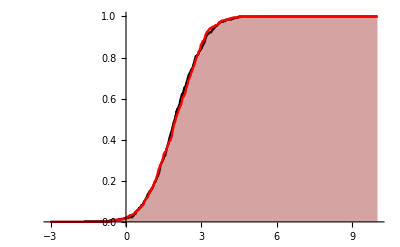

```mathematica
Show[{DiscretePlot[CDF[empf1,x],{x,-3,10,.01},PlotStyle->Black],DiscretePlot[CDF[empf2,x],{x,-3,10,.01},PlotStyle->Red]}]
```

```mathematica
coef=√((40*70)/(40+70))//N;
ϵ=0.5;
δ=ϵ/coef
```

0.0991031

```mathematica
Table[{x,∑_(i=-∞)^∞ (-1)^i ⅇ^(-2 i^2 x^2)},{x,0.4,2,.05}]//N
```

{{0.4,0.00280767},{0.45,0.0125894},{0.5,0.0360548},{0.55,0.0771832},{0.6,0.135717},{0.65,0.207987},{0.7,0.288765},{0.75,0.372833},{0.8,0.455858},{0.85,0.534681},{0.9,0.607269},{0.95,0.672515},{1.,0.73},{1.05,0.779794},{1.1,0.822282},{1.15,0.85804},{1.2,0.88775},{1.25,0.912134},{1.3,0.931908},{1.35,0.947758},{1.4,0.960318},{1.45,0.970159},{1.5,0.977782},{1.55,0.983623},{1.6,0.988048},{1.65,0.991364},{1.7,0.993823},{1.75,0.995625},{1.8,0.996932},{1.85,0.99787},{1.9,0.998536},{1.95,0.999004},{2.,0.999329}}

```mathematica
1-0.0125894
```

0.987411

```mathematica
Max@Table[Abs[CDF[empf1,x]-CDF[empf2,x]],{x,-3,10,.1}]
```

0.139286

#### Simulation

```mathematica
simulation[exp_,var_,n_,m_,ϵ_,k_]:=Module[{data1,data2,empf1,empf2,results={},δ},δ=ϵ/√((n*m)/(n+m));Do[data1=RandomVariate[NormalDistribution[exp,var],n];data2=RandomVariate[NormalDistribution[exp,var],m];empf1=EmpiricalDistribution[data1];
empf2=EmpiricalDistribution[data2];AppendTo[results,Max[Table[Abs[CDF[empf1,x]-CDF[empf2,x]],{x,-3,10,.1}]]>δ],k];results]
```

```mathematica
res=simulation[3,2,300,350,0.45,100];
```

```mathematica
Count[res,True]/Length@res//N
```

0.96

```mathematica
Table[newRes=simulation[3,2,600,700,0.45,100];Count[newRes,True]/Length@newRes//N,10]
```

{0.94,0.96,0.94,0.95,0.98,0.94,0.96,0.95,0.94,0.95}

```mathematica
0.45/√((600*700)/(600+700))
```

0.0250357

```mathematica
res
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,False,True,True,True,True,True,False,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Count[res,True]
```

96